```mathematica
Exp[I*π/4]
```

ⅇ^((ⅈ π)/4)

```mathematica
N[ⅇ^((ⅈ π)/4)]
```

0.707107+0.707107 ⅈ

```mathematica
Clear[m,M,A,B,c,a]
```

```mathematica
Det[({{m*w^2-4/3*c+A*(4*Cos[k/2*a]-4), 0, 0, 4/3*c*Cos[k/4*a], 0, 0}, {0, m*w^2-4/3*c+A*(2*Cos[k/2*a]-2), 0, 0, 4/3*c*Cos[k/4*a], -I*4/3*c*Sin[k/4*a]}, {0, 0, m*w^2-4/3*c+A*(2*Cos[k/2*a]-2), 0, -I*4/3*c*Sin[k/4*a], 4/3*c*Cos[k/4*a]}, {4/3*c*Cos[k/4*a], 0, 0, M*w^2-4/3*c+B*(4*Cos[k/2*a]-4), 0, 0}, {0, 4/3*c*Cos[k/4*a], I*4/3*c*Sin[k/4*a], 0, M*w^2-4/3*c+B*(2*Cos[k/2*a]-2), 0}, {0, I*4/3*c*Sin[k/4*a], 4/3*c*Cos[k/4*a], 0, 0, M*w^2-4/3*c+B*(2*Cos[k/2*a]-2)}})]
```

1/729 (-16 c^2 Cos[(a k)/4]^2 ((-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) ((-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-16 c^2 Cos[(a k)/4]^2+(-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]))-16 c^2 (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) Sin[(a k)/4]^2)+4 c Cos[(a k)/4] (-4 c Cos[(a k)/4] (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2])+4 c Cos[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2))-4 ⅈ c Sin[(a k)/4] (-4 ⅈ c (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) Sin[(a k)/4]+4 ⅈ c Sin[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2)))+(-12 A-4 c+3 m w^2+12 A Cos[(a k)/2]) (-12 B-4 c+3 M w^2+12 B Cos[(a k)/2]) ((-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) ((-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-16 c^2 Cos[(a k)/4]^2+(-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]))-16 c^2 (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) Sin[(a k)/4]^2)+4 c Cos[(a k)/4] (-4 c Cos[(a k)/4] (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2])+4 c Cos[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2))-4 ⅈ c Sin[(a k)/4] (-4 ⅈ c (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) Sin[(a k)/4]+4 ⅈ c Sin[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2))))

```mathematica
Solve[1/729 (-16 c^2 Cos[(a k)/4]^2 ((-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) ((-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-16 c^2 Cos[(a k)/4]^2+(-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]))-16 c^2 (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) Sin[(a k)/4]^2)+4 c Cos[(a k)/4] (-4 c Cos[(a k)/4] (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2])+4 c Cos[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2))-4 ⅈ c Sin[(a k)/4] (-4 ⅈ c (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) Sin[(a k)/4]+4 ⅈ c Sin[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2)))+(-12 A-4 c+3 m w^2+12 A Cos[(a k)/2]) (-12 B-4 c+3 M w^2+12 B Cos[(a k)/2]) ((-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) ((-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-16 c^2 Cos[(a k)/4]^2+(-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]))-16 c^2 (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) Sin[(a k)/4]^2)+4 c Cos[(a k)/4] (-4 c Cos[(a k)/4] (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2])+4 c Cos[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2))-4 ⅈ c Sin[(a k)/4] (-4 ⅈ c (-6 A-4 c+3 m w^2+6 A Cos[(a k)/2]) (-6 B-4 c+3 M w^2+6 B Cos[(a k)/2]) Sin[(a k)/4]+4 ⅈ c Sin[(a k)/4] (16 c^2 Cos[(a k)/4]^2+16 c^2 Sin[(a k)/4]^2))))==0(*&&m>0&&M>0*),w]
```

{{w→-√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M-1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→-√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M-1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M-1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M-1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→-√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M+1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→-√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M+1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M+1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M+1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))},{w→-√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M-1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))},{w→√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M-1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))},{w→-√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M+1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))},{w→√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M+1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))}}

```mathematica
Clear[m,M,A,B,c,a]
k=0
f[k]=√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M-1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))
g[k]=√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M+1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))
t[k]=√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M-1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))
n[k]=√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M+1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))
Clear[k]
```

0

√((2 c)/(3 m)+(2 c)/(3 M)-(√((-4 c m-4 c M)^2))/(6 m M))

√((2 c)/(3 m)+(2 c)/(3 M)+(√((-4 c m-4 c M)^2))/(6 m M))

√((2 c)/(3 m)+(2 c)/(3 M)-(√((-12 c m-12 c M)^2))/(18 m M))

√((2 c)/(3 m)+(2 c)/(3 M)+(√((-12 c m-12 c M)^2))/(18 m M))

```mathematica
a=1
m=1
M=65/32
A=1
B=1
c=1
```

1

1

65/32

1

1

1

```mathematica
(*f和t为声学支，g、n为光学支*)
```

```mathematica
f[k]=√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M-1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))
g[k]=√(A/m+(2 c)/(3 m)+B/M+(2 c)/(3 M)-(A Cos[(a k)/2])/m-(B Cos[(a k)/2])/M+1/(6 m M)(√((-6 B m-4 c m-6 A M-4 c M+6 B m Cos[(a k)/2]+6 A M Cos[(a k)/2])^2-12 m M (18 A B+8 A c+8 B c-24 A B Cos[(a k)/2]-8 A c Cos[(a k)/2]-8 B c Cos[(a k)/2]+6 A B Cos[a k]))))
t[k]=√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M-1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))
n[k]=√((2 A)/m+(2 c)/(3 m)+(2 B)/M+(2 c)/(3 M)-(2 A Cos[(a k)/2])/m-(2 B Cos[(a k)/2])/M+1/(18 m M)(√((-36 B m-12 c m-36 A M-12 c M+36 B m Cos[(a k)/2]+36 A M Cos[(a k)/2])^2-36 m M (216 A B+48 A c+48 B c+8 c^2-288 A B Cos[(a k)/2]-48 A c Cos[(a k)/2]-48 B c Cos[(a k)/2]-8 c^2 Cos[(a k)/2]+72 A B Cos[a k]))))
```

√(97/39-97/65 Cos[k/2]-16/195 √((-485/16+291/16 Cos[k/2])^2-195/8 (34-40 Cos[k/2]+6 Cos[k])))

√(97/39-97/65 Cos[k/2]+16/195 √((-485/16+291/16 Cos[k/2])^2-195/8 (34-40 Cos[k/2]+6 Cos[k])))

√(776/195-194/65 Cos[k/2]-16/585 √((-291/2+873/8 Cos[k/2])^2-585/8 (320-392 Cos[k/2]+72 Cos[k])))

√(776/195-194/65 Cos[k/2]+16/585 √((-291/2+873/8 Cos[k/2])^2-585/8 (320-392 Cos[k/2]+72 Cos[k])))

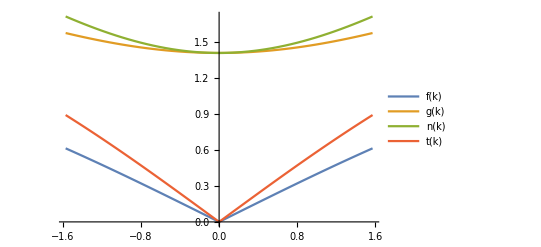

Null

```mathematica
Plot[{f[k],g[k],n[k],t[k]},{k,-π/(2*a),π/(2*a)},PlotLegends->"Expressions"]
```

```mathematica
Clear[A,B,a]
f[x,y,z]=(Sin[x*a/2]*Cos[(y+z)*a/4]*Cos[(y-z)*a/4])/(√(A+B*((Cos[x*a/4]*Cos[y*a/4]*Cos[z*a/4])^2+(Sin[x*a/4]*Sin[y*a/4]*Sin[z*a/4])^2)))
Grad[f[x,y,z],{x,y,z}]
```

(Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] Sin[(a x)/2])/(√(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))

{-(B Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] Sin[(a x)/2] (-1/2 a Cos[(a x)/4] Cos[(a y)/4]^2 Cos[(a z)/4]^2 Sin[(a x)/4]+1/2 a Cos[(a x)/4] Sin[(a x)/4] Sin[(a y)/4]^2 Sin[(a z)/4]^2))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[(a x)/2] Cos[1/4 a (y-z)] Cos[1/4 a (y+z)])/(2 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))),-(B Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] Sin[(a x)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a y)/4]+1/2 a Cos[(a y)/4] Sin[(a x)/4]^2 Sin[(a y)/4] Sin[(a z)/4]^2))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))-(a Cos[1/4 a (y+z)] Sin[(a x)/2] Sin[1/4 a (y-z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (y-z)] Sin[(a x)/2] Sin[1/4 a (y+z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))),-(B Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] Sin[(a x)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4] Sin[(a z)/4]+1/2 a Cos[(a z)/4] Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[1/4 a (y+z)] Sin[(a x)/2] Sin[1/4 a (y-z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (y-z)] Sin[(a x)/2] Sin[1/4 a (y+z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))}

```mathematica
(*xx*)
```

```mathematica
Simplify[-(B Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] Sin[(a x)/2] (-1/2 a Cos[(a x)/4] Cos[(a y)/4]^2 Cos[(a z)/4]^2 Sin[(a x)/4]+1/2 a Cos[(a x)/4] Sin[(a x)/4] Sin[(a y)/4]^2 Sin[(a z)/4]^2))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[(a x)/2] Cos[1/4 a (y-z)] Cos[1/4 a (y+z)])/(2 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))]
```

(a Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] (B (Cos[(a y)/2]+Cos[(a z)/2]) Sin[(a x)/2]^2+8 Cos[(a x)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
Subscript[E, xx]=2*a*Subscript[J, AB]^2*((a Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] (B (Cos[(a y)/2]+Cos[(a z)/2]) Sin[(a x)/2]^2+8 Cos[(a x)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
```

(a^2 Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] (B (Cos[(a y)/2]+Cos[(a z)/2]) Sin[(a x)/2]^2+8 Cos[(a x)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
(*xy*)
```

```mathematica
Simplify[-(B Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] Sin[(a x)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a y)/4]+1/2 a Cos[(a y)/4] Sin[(a x)/4]^2 Sin[(a y)/4] Sin[(a z)/4]^2))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))-(a Cos[1/4 a (y+z)] Sin[(a x)/2] Sin[1/4 a (y-z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (y-z)] Sin[(a x)/2] Sin[1/4 a (y+z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))]
```

-((a Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])))/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))

```mathematica
Subscript[E, xy]=Subscript[E, yx]= -2*a*Subscript[J, AB]^2*((a Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])))/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
```

-((a^2 Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])) J_AB^2)/(4 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))

```mathematica
(*xz*)
Simplify[-(B Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] Sin[(a x)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4] Sin[(a z)/4]+1/2 a Cos[(a z)/4] Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[1/4 a (y+z)] Sin[(a x)/2] Sin[1/4 a (y-z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (y-z)] Sin[(a x)/2] Sin[1/4 a (y+z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))]
```

(a Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
Subscript[E, xz]=Subscript[E, zx]=2*a*Subscript[J, AB]^2*(a Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))
```

(a^2 Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
g[x,y,z]=(Sin[y*a/2]*Cos[(x+z)*a/4]*Cos[(x-z)*a/4])/(√(A+B*((Cos[x*a/4]*Cos[y*a/4]*Cos[z*a/4])^2+(Sin[x*a/4]*Sin[y*a/4]*Sin[z*a/4])^2)))
Grad[g[x,y,z],{x,y,z}]
```

(Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] Sin[(a y)/2])/(√(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))

{-(B Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] Sin[(a y)/2] (-1/2 a Cos[(a x)/4] Cos[(a y)/4]^2 Cos[(a z)/4]^2 Sin[(a x)/4]+1/2 a Cos[(a x)/4] Sin[(a x)/4] Sin[(a y)/4]^2 Sin[(a z)/4]^2))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))-(a Cos[1/4 a (x+z)] Sin[(a y)/2] Sin[1/4 a (x-z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (x-z)] Sin[(a y)/2] Sin[1/4 a (x+z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))),-(B Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] Sin[(a y)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a y)/4]+1/2 a Cos[(a y)/4] Sin[(a x)/4]^2 Sin[(a y)/4] Sin[(a z)/4]^2))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[(a y)/2] Cos[1/4 a (x-z)] Cos[1/4 a (x+z)])/(2 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))),-(B Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] Sin[(a y)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4] Sin[(a z)/4]+1/2 a Cos[(a z)/4] Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[1/4 a (x+z)] Sin[(a y)/2] Sin[1/4 a (x-z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (x-z)] Sin[(a y)/2] Sin[1/4 a (x+z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))}

```mathematica
(*yy*)
```

```mathematica
Simplify[-(B Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] Sin[(a y)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a y)/4]+1/2 a Cos[(a y)/4] Sin[(a x)/4]^2 Sin[(a y)/4] Sin[(a z)/4]^2))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[(a y)/2] Cos[1/4 a (x-z)] Cos[1/4 a (x+z)])/(2 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))]
```

(a Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] (B (Cos[(a x)/2]+Cos[(a z)/2]) Sin[(a y)/2]^2+8 Cos[(a y)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
Subscript[E, yy]=2*a*Subscript[J, AB]^2*((a Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] (B (Cos[(a x)/2]+Cos[(a z)/2]) Sin[(a y)/2]^2+8 Cos[(a y)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
```

(a^2 Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] (B (Cos[(a x)/2]+Cos[(a z)/2]) Sin[(a y)/2]^2+8 Cos[(a y)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
(*yz*)
Simplify[-(B Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] Sin[(a y)/2] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4] Sin[(a z)/4]+1/2 a Cos[(a z)/4] Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]))/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[1/4 a (x+z)] Sin[(a y)/2] Sin[1/4 a (x-z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (x-z)] Sin[(a y)/2] Sin[1/4 a (x+z)])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))]
```

(a Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
Subscript[E, yz]=Subscript[E, zy]=2*a*Subscript[J, AB]^2*(a Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))
```

(a^2 Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
h[x,y,z]=(Sin[z*a/2]*Cos[(x+y)*a/4]*Cos[(x-y)*a/4])/(√(A+B*((Cos[x*a/4]*Cos[y*a/4]*Cos[z*a/4])^2+(Sin[x*a/4]*Sin[y*a/4]*Sin[z*a/4])^2)))
Grad[h[x,y,z],{x,y,z}]
```

(Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] Sin[(a z)/2])/(√(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))

{-(B Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (-1/2 a Cos[(a x)/4] Cos[(a y)/4]^2 Cos[(a z)/4]^2 Sin[(a x)/4]+1/2 a Cos[(a x)/4] Sin[(a x)/4] Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[(a z)/2])/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))-(a Cos[1/4 a (x+y)] Sin[1/4 a (x-y)] Sin[(a z)/2])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (x-y)] Sin[1/4 a (x+y)] Sin[(a z)/2])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))),-(B Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a y)/4]+1/2 a Cos[(a y)/4] Sin[(a x)/4]^2 Sin[(a y)/4] Sin[(a z)/4]^2) Sin[(a z)/2])/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))+(a Cos[1/4 a (x+y)] Sin[1/4 a (x-y)] Sin[(a z)/2])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(a Cos[1/4 a (x-y)] Sin[1/4 a (x+y)] Sin[(a z)/2])/(4 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))),(a Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] Cos[(a z)/2])/(2 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(B Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4] Sin[(a z)/4]+1/2 a Cos[(a z)/4] Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]) Sin[(a z)/2])/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))}

```mathematica
(*zz*)
Simplify[(a Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] Cos[(a z)/2])/(2 √(A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))-(B Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (-1/2 a Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4] Sin[(a z)/4]+1/2 a Cos[(a z)/4] Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]) Sin[(a z)/2])/(2 (A+B (Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))^(3/2))]
Subscript[E, zz]=2*a*Subscript[J, AB]^2*((a Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (8 Cos[(a z)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Sin[(a z)/2]^2))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
```

(a Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (8 Cos[(a z)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Sin[(a z)/2]^2))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

(a^2 Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (8 Cos[(a z)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Sin[(a z)/2]^2) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
Subscript[E, xx]=2*a*Subscript[J, AB]^2*((a Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] (B (Cos[(a y)/2]+Cos[(a z)/2]) Sin[(a x)/2]^2+8 Cos[(a x)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
Subscript[E, xy]=Subscript[E, yx]= -2*a*Subscript[J, AB]^2*((a Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])))/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
Subscript[E, xz]=Subscript[E, zx]=2*a*Subscript[J, AB]^2*(a Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))
Subscript[E, yy]=2*a*Subscript[J, AB]^2*((a Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] (B (Cos[(a x)/2]+Cos[(a z)/2]) Sin[(a y)/2]^2+8 Cos[(a y)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
Subscript[E, yz]=Subscript[E, zy]=2*a*Subscript[J, AB]^2*(a Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))
Subscript[E, zz]=2*a*Subscript[J, AB]^2*((a Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (8 Cos[(a z)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Sin[(a z)/2]^2))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))
```

(a^2 Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] (B (Cos[(a y)/2]+Cos[(a z)/2]) Sin[(a x)/2]^2+8 Cos[(a x)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

-((a^2 Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])) J_AB^2)/(4 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)))

(a^2 Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

(a^2 Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] (B (Cos[(a x)/2]+Cos[(a z)/2]) Sin[(a y)/2]^2+8 Cos[(a y)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

(a^2 Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

(a^2 Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (8 Cos[(a z)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Sin[(a z)/2]^2) J_AB^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))

```mathematica
x=π/a
y=π/a
z=π/a
```

π/a

π/a

π/a

```mathematica
({{2*a*Subscript[J, AB]^2*((a Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] (B (Cos[(a y)/2]+Cos[(a z)/2]) Sin[(a x)/2]^2+8 Cos[(a x)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), -2*a*Subscript[J, AB]^2*((a Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])))/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), 2*a*Subscript[J, AB]^2*(a Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))}, {-2*a*Subscript[J, AB]^2*((a Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])))/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), 2*a*Subscript[J, AB]^2*((a Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] (B (Cos[(a x)/2]+Cos[(a z)/2]) Sin[(a y)/2]^2+8 Cos[(a y)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), 2*a*Subscript[J, AB]^2*(a Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))}, {2*a*Subscript[J, AB]^2*(a Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)), 2*a*Subscript[J, AB]^2*(a Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)), (a^2 Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (8 Cos[(a z)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Sin[(a z)/2]^2) Subscript[J, AB]^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))}})
```

{{0,-(a^2 J_AB^2)/(2 √(A+B/4)),-(a^2 J_AB^2)/(2 √(A+B/4))},{-(a^2 J_AB^2)/(2 √(A+B/4)),0,-(a^2 J_AB^2)/(2 √(A+B/4))},{-(a^2 J_AB^2)/(2 √(A+B/4)),-(a^2 J_AB^2)/(2 √(A+B/4)),0}}

```mathematica
Eigenvalues[({{2*a*Subscript[J, AB]^2*((a Cos[1/4 a (y-z)] Cos[1/4 a (y+z)] (B (Cos[(a y)/2]+Cos[(a z)/2]) Sin[(a x)/2]^2+8 Cos[(a x)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), -2*a*Subscript[J, AB]^2*((a Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])))/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), 2*a*Subscript[J, AB]^2*(a Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))}, {-2*a*Subscript[J, AB]^2*((a Sin[(a x)/2] (Cos[1/4 a (y+z)] (B Cos[1/4 a (y-z)] Sin[(a x)/4]^2 Sin[(a y)/2] Sin[(a z)/4]^2+2 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2))+2 Cos[1/4 a (y-z)] (B Cos[(a x)/4]^2 Cos[(a y)/4] Cos[(a z)/4]^2 Sin[(a z)/4]+(A+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)])))/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), 2*a*Subscript[J, AB]^2*((a Cos[1/4 a (x-z)] Cos[1/4 a (x+z)] (B (Cos[(a x)/2]+Cos[(a z)/2]) Sin[(a y)/2]^2+8 Cos[(a y)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))), 2*a*Subscript[J, AB]^2*(a Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))}, {2*a*Subscript[J, AB]^2*(a Sin[(a x)/2] (Cos[1/4 a (y+z)] (4 Sin[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (y-z)] Sin[(a z)/2])-4 Cos[1/4 a (y-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (y+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)), 2*a*Subscript[J, AB]^2*(a Sin[(a y)/2] (Cos[1/4 a (x+z)] (4 Sin[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Cos[1/4 a (x-z)] Sin[(a z)/2])-4 Cos[1/4 a (x-z)] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2) Sin[1/4 a (x+z)]))/(16 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2)), (a^2 Cos[1/4 a (x-y)] Cos[1/4 a (x+y)] (8 Cos[(a z)/2] (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)+B (Cos[(a x)/2]+Cos[(a y)/2]) Sin[(a z)/2]^2) Subscript[J, AB]^2)/(8 (A+B Cos[(a x)/4]^2 Cos[(a y)/4]^2 Cos[(a z)/4]^2+B Sin[(a x)/4]^2 Sin[(a y)/4]^2 Sin[(a z)/4]^2)^(3/2))}})]
```

{-(2 a^2 J_AB^2)/(√(4 A+B)),(a^2 J_AB^2)/(√(4 A+B)),(a^2 J_AB^2)/(√(4 A+B))}

```mathematica
Simplify[(Sin^2)[u/2]*(Cos^4)[v/4]+(Sin^2)[v/2]*(Cos^4)[u/4]]
```

Cos^4[v/4] Sin^2[u/2]+Cos^4[u/4] Sin^2[v/2]